```mathematica
(*  
  Tanker Refueling Scheduler with Altitude Assignment
 This version allows horizontal combinations of two anchors.

Author: Bruce Sawhill <brucesawhill@gmail.com>
*)
```

```mathematica
(* Function Definitions *)
```

```mathematica
timeparse[timestring_]:=
Module[{dayvalue,hourvalue,minutevalue,totalminutes}, (* works for demand format *)
{dayvalue=ToExpression[StringTake[timestring,3]];
hourvalue =ToExpression[StringTake[timestring,{5,6}]];
minutevalue = ToExpression[StringTake[timestring,-2]];
totalminutes = 1440 dayvalue + 60 hourvalue + minutevalue
}[[1]]
]
```

```mathematica
reversetimeparse[minfromzero_, datestring_]:=
Module[{hour,minute,hourmilform,minutemilform,hourstring,minutestring,output},
{hour=Quotient[minfromzero,60];
minute=Mod[minfromzero,60];
hourmilform={Quotient[hour,10],Mod[hour,10]};
minutemilform={Quotient[minute,10],Mod[minute,10]};
hourstring=StringJoin[ToString[hourmilform[[1]]],ToString[hourmilform[[2]]]];
minutestring=StringJoin[ToString[minutemilform[[1]]],
ToString[minutemilform[[2]]]];
output=StringJoin[datestring," ",hourstring," ",minutestring]
}
]
```

```mathematica
daysadd[timestring_,numdays_]:=
Module[{dayvalue,newdayvalue,daystring,newstring},
(*adds days to time given in day hour min format*)
(* Does not change month value! *)
{dayvalue=ToExpression[StringTake[timestring,3]];
newdayvalue=dayvalue+numdays;
daystring=StringJoin["0",ToString[Quotient[newdayvalue,10]], ToString[Mod[newdayvalue,10]]];
newstring=StringJoin[daystring, StringTake[timestring,{4,-1}]]
}[[1]]
]
```

```mathematica
Clear[theaterdemand]
```

```mathematica
theaterdemand[anchorparseddemand_]:=
(* Format: {anch, #_anch,t1,t2,alt,RFID,N1,N2,ID3,ID4,Fuel,#_theater} *)
Sort[(* time is 000 hrs at beginning of data day *)
Flatten[(* data ordered by RF start time (t1) *)
Table[
Flatten[
{anchno,i,timeparse[anchorparseddemand[[anchno,i,2]]]-23 1440,
timeparse[anchorparseddemand[[anchno,i,3]]]-23 1440,Take[anchorparseddemand[[anchno,i]],{4,10}]},1
],{anchno, Length[anchorparseddemand]},{i,Length[anchorparseddemand[[anchno]]]}
],1
],#2[[3]]>#1[[3]]&
];
```

```mathematica
dayshift[anchordemand_,numdays_]:=
Module[{demcopy},
{demcopy = anchordemand;
Do[
{
demcopy[[j,2]]=daysadd[demcopy[[j,2]],numdays];
demcopy[[j,3]]=daysadd[demcopy[[j,3]],numdays]
}
,{j,Length[demcopy]}]
};
demcopy
]
```

```mathematica
createanchorstring[anchno_]:=
(* Create anchor identifier string of one or two digits *)
{StringJoin["ANCH", ToString[Quotient[anchno,10]],ToString[Mod[anchno,10]]]
}[[1]]
```

```mathematica
parselatlong[llstring_]:=
(* For demand format *)
ToExpression[
{StringTake[llstring,{1,2}],
StringTake[llstring,{3,4}],
StringTake[llstring, {6,8}],StringTake[llstring, {9,10}]
}
]
```

```mathematica
convertplltodecimal[latlongvector_]:={latlongvector[[1]]+latlongvector[[2]]/60.,latlongvector[[3]]+latlongvector[[4]]/60.}
```

```mathematica
firstavailbyanchor[anchorRFlist_,mininterval_,maxwait_]:=
Module[{lRF,falist,timebetween,j},
(* Gives next RF event that can be combined with indexed event,
parsed by anchor *)
{lRF=Length[anchorRFlist];
falist=Table[0,{lRF}];
falist[[-1]]={};
Do[
j=i+1;
While[j<lRF &&anchorRFlist[[j,3]]-anchorRFlist[[i,4]]<mininterval , j+=1];
falist[[i]]=If[anchorRFlist[[j,3]]-anchorRFlist[[i,4]]>maxwait ||j>lRF,{}, j],{i,Length[anchorRFlist]-1}
];
falist
}[[1]]
]
```

```mathematica
firstavailbytheater[theaterRFlist_,mininterval_,maxwait_]:=
Module[{lRF,falist,j},
(* Gives next RF event that can be combined with indexed event, testing for same anchor *)
{lRF=Length[theaterRFlist];
falist=Table[0,{lRF}];
falist[[-1]]={};
Do[
j=i+1;
While[j<lRF &&(theaterRFlist[[j,3]]-theaterRFlist[[i,4]]<mininterval || theaterRFlist[[j,1]]!=theaterRFlist[[i,1]]), j+=1];
falist[[i]]=If[theaterRFlist[[j,3]]-theaterRFlist[[i,4]]>maxwait ||j>lRF,{}, j],{i,Length[theaterRFlist]-1}
];
falist
}[[1]]
]
```

```mathematica
firstavailbytheater2[theaterRFlist_,mininterval_,maxwait_]:=
Module[{lRF,falist,j},
(* Gives next RF event that can be combined with indexed event, testing for same anchor *)
{lRF=Length[theaterRFlist];
falist=Table[{},{lRF}];
(*falist[[-1]]={};*)
Do[
j=i+1;
While[j<=lRF &&(theaterRFlist[[j,3]]-theaterRFlist[[i,4]]<mininterval || theaterRFlist[[j,1]]!=theaterRFlist[[i,1]]), j+=1];
If[j>lRF, falist[[i]]={},falist[[i]]=If[theaterRFlist[[j,3]]-theaterRFlist[[i,4]]>maxwait,{}, j]],{i,Length[theaterRFlist]-1}
];
falist
}[[1]]
]
```

Fuel burn model obtained from mining aropOffload();  Value does not include offloaded fuel, it is fuel burned by tanker during offload process.

```mathematica
fuelburnfn[m_,t_,off_]:=127.553-.00487364 off+143.878 t + .0000994124 m t+8.2217 10^(-10) m^2 t
```

Same with all input masses in klbs, output still in lbs.

```mathematica
fuelburnkfn[m_,t_,off_]:=(127.553-4.87364 off+143.878 t + .0994124 m t+8.2217 10^(-4) m^2 t)/1000.
```

```mathematica
rftimeintervals[refuellist_]:= (* time intervals betwen end of one
refueling event and start of another. Only really useful for anchor-based calculations, not theater-wide *)
Table[refuellist[[j,3]]-refuellist[[i,4]],{i,Length[refuellist]},{j,Length[refuellist]}];
```

```mathematica
rftimeintervals2[refuellist_,arg1_,arg2_]:=
Module[{diff},(* Faster version of first function *)
{diff=refuellist[[arg2,3]]-refuellist[[arg1,4]];
};
diff
]
```

```mathematica
mmaholdoffload[timeholdbefore_,timeoffload_,initialweight_,offloadamt_]:=
Module[{loiterburn,afterloiterweight,deltaoffload},
{loiterburn=fuelburnfn[initialweight,timeholdbefore,0];
afterloiterweight=initialweight-loiterburn;
deltaoffload=fuelburnfn[afterloiterweight,timeoffload,offloadamt];
};
loiterburn+deltaoffload+offloadamt
]
```

```mathematica
mmaholdoffloadk[timeholdbefore_,timeoffload_,initialweight_,offloadamt_]:=
Module[{loiterburn,afterloiterweight,deltaoffload},
{loiterburn=fuelburnkfn[initialweight,timeholdbefore,0];
afterloiterweight=initialweight-loiterburn;
deltaoffload=fuelburnkfn[afterloiterweight,timeoffload,offloadamt];
};
loiterburn+deltaoffload+offloadamt
]
```

```mathematica
tailassign[eventlist_,basecaps_]:=
Module[
{baseindices,baseindex,nexttail,nbi,tailnumarray,availtailnums,neweventlist,pos},

{(* Initialization *)
baseindices=Union[Table[eventlist[[i,2]],{i,Length[eventlist]}]];
nbi=Length[baseindices];
tailnumarray=Table[{},{nbi}];
availtailnums=Table[j, {i,Length[basecaps]},{j,basecaps[[i]]}];
neweventlist=eventlist;

Do[
{(* Local variables for each event *)
baseindex=Position[baseindices,eventlist[[k,2]]][[1,1]];
(* Print["baseindex = ", baseindex];*)
nexttail=availtailnums[[baseindex,1]]; (* first available tail at base *)
(* Print["nexttail = ", nexttail];*)

If[(* If a mission launches, pop the tail number stack for assignment, recycled ones first *)
eventlist[[k,5]]==-1,
{
AppendTo[
tailnumarray[[baseindex]],{nexttail,eventlist[[k,1]]}
];
AppendTo[neweventlist[[k]],nexttail];
pos=Position[Table[neweventlist[[k,1]],{k,Length[neweventlist]}],eventlist[[k,1]]];
pos=Table[pos[[i,1]],{i,Length[pos]}];
(* Print["positions = ",pos];*)
Do[AppendTo[neweventlist[[pos[[i]]]],nexttail],{i,Length[pos]}];
availtailnums[[baseindex]]=DeleteCases[availtailnums[[baseindex]],nexttail];
(* Print["availtailnums[[",baseindex,"]]= ", availtailnums[[baseindex]]]*)
}
];

If[(* If an A/C has been at base long enough to turn, add to availables *)
eventlist[[k,5]]==2,
{availtailnums[[baseindex]]=Sort[AppendTo[availtailnums[[baseindex]],neweventlist[[k,6]]]]
(* Print["Here"];
Print["availtailnums = ",availtailnums];*)
}
];
}
,{k,Length[eventlist]}
]
};
{tailnumarray, neweventlist}
]
```

```mathematica
fastbase[eventlist_,cutofftime_]:=
Module[{eventshortform,netdeploys,i},
{eventshortform=Sort[Table[eventlist[[j,{2,4,5}]],{j,Length[eventlist]}],#2[[2]]>#1[[2]]&];
netdeploys=Table[0,{i,5}];

i=1;
While[(* Base accounting *)
eventshortform[[i,2]]<cutofftime && i≤ Length[eventlist],
{
If[eventshortform[[i,3]]==-1, 
netdeploys[[eventshortform[[i,1]]]]+=1
];
If[eventshortform[[i,3]]==2,
netdeploys[[eventshortform[[i,1]]]]+=-1
];
If[i==Length[eventlist],Break[]];
i+=1
}
]
};
netdeploys
];
```

```mathematica
dynamicbaseassign[deploys_,basecaps_,basepreforder_]:=
Module[{assignedbase},
{i=1;
While[deploys[[basepreforder[[i]]]]≥basecaps[[basepreforder[[i]]]],
i++
];
assignedbase=basepreforder[[i]]
};
assignedbase
]
```

```mathematica
totaltails[tailassignlist_]:=
Module[{maxvector},
{maxvector=Table[0,{5}];
Do[maxvector[[i]]=Max[Table[tailassignlist[[i,j,1]],{j,Length[tailassignlist[[i]]]}]]
,{i,5}]
};
Plus@@maxvector
]
```

```mathematica
(* Data Preprocessing *)
```

```mathematica
elapsedtimeformat[totalminutes_]:=
Module[{m,h,hs,ms},
{h=If[totalminutes<1440, Quotient[totalminutes,60],Quotient[Mod[totalminutes,1440],60]];
h=Floor[h];
hs=If[h<10,StringJoin[ToString[0],ToString[h]],ToString[h]],
m=Mod[totalminutes,60];
m=Floor[m];
ms=If[m<10, StringJoin[ToString[0],ToString[m]],ToString[m]];
result=StringJoin[hs,":",ms]
};
result
]
```

```mathematica
miltimeformat[startmonth_,startday_,minutes_]:=
Module[{monthdays,minutesinmonth,daynum,minnum,hournum,remainminutes,hourstring,minutestring},
{monthdays=Switch[
startmonth,1,{"JAN",31},2,{"FEB",28},3,{"MAR",31},
4,{"APR",30},5,{"MAY",31},6,{"JUN",30},
7,{"JUL",31},8,{"AUG",31},9,{"SEP",31},
10,{"OCT",31},11,{"NOV",31},12,{"DEC",31}];
minutesinmonth=startday  1440+minutes;
daynum=Quotient[minutesinmonth,1440];
minnum=Mod[minutesinmonth,1440];
hournum=Quotient[minnum,60];
hourstring=If[hournum<10,StringJoin["0",ToString[hournum]],ToString[hournum]];
minnum=Mod[minnum,60];
minutestring=If[minnum<10,StringJoin["0",ToString[minnum]],ToString[minnum]];
};
StringJoin[monthdays[[1]]," ", ToString[daynum], " ",hourstring,":",minutestring]
]
```

```mathematica
fuelbasetoanchor[anchorbasepair_,anchoralt_]:=aabtf[[If[anchoralt>14000,anchoralt/1000-14,1],anchorbasepair[[2]],anchorbasepair[[1]],2]]
```

```mathematica
timebasetoanchor[anchorbasepair_,anchoralt_]:=aabtf[[If[anchoralt>14000,anchoralt/1000-14,1],anchorbasepair[[2]],anchorbasepair[[1]],1]]
```

```mathematica
assembletheatersorties[tankerRFs_, theaterdemand_,altitudes_]:=
Module[{lRF,rfevents,startrf,endrf},
{
lRF=Length[tankerRFs];
(*rfevent format: {base (outbound/inbound legs) or anchor,
startrf,endrf,altitude,offloadfuel,startfuel,endfuel*)
rfevents=Table[Table[0,{k,16}],{i,lRF},{j,Length[tankerRFs[[i,2]]]+2}];(* 16 column table *)
Print["numsorties = ",lRF];
Do[
{startrf=theaterdemand[[tankerRFs[[i,2,1]],3]];
endrf=theaterdemand[[tankerRFs[[i,2,-1]],4]];
rfevents[[i,1,1]]=baselocs[[tankerRFs[[i,3,1]],3]];
rfevents[[i,1,2]]="";
rfevents[[i,1,3]]="";
rfevents[[i,-1,2]]=baselocs[[tankerRFs[[i,3,1]],3]];
rfevents[[i,-1,1]]="";
rfevents[[i,-1,3]]="";

Do[
{rfevents[[i,j+1]]={"","" ,anchorlist[[tankerRFs[[i,3,2]],1]],theaterdemand[[tankerRFs[[i,2,j]],3]],
theaterdemand[[tankerRFs[[i,2,j]],4]],altitudes[[i]],
theaterdemand[[tankerRFs[[i,2,j]],11]],0,0,0,0,0,
theaterdemand[[tankerRFs[[i,2,j]],6]]
(*pd[[anchorindex,results[[anchorindex]][[1,1,i,j]],5]]*),theaterdemand[[tankerRFs[[i,2,j]],8]],theaterdemand[[tankerRFs[[i,2,j]],10]],theaterdemand[[tankerRFs[[i,2,j]],9]]
};
}, {j,Length[tankerRFs[[i,2]]]}
];

rfevents[[i,2,9]]=200000-fuelbasetoanchor[tankerRFs[[i,3]],altitudes[[i]]];
rfevents[[i,1,4]]=rfevents[[i,2,4]]-timebasetoanchor[tankerRFs[[i,3]],altitudes[[i]]]-10;
rfevents[[i,1,5]]=rfevents[[i,2,4]]-10;
rfevents[[i,1,9]]=200000.;
rfevents[[i,1,10]]=rfevents[[i,2,9]]
},{i,1,lRF}
];
};
rfevents
]
```

```mathematica
assembletheatersortiesconsout[tankerRFs_, theaterdemand_,altitudes_,consvector_]:=
Module[{lRF,rfevents,startrf,endrf},
{
lRF=Length[tankerRFs];
(*rfevent format: {base (outbound/inbound legs) or anchor,
startrf,endrf,altitude,offloadfuel,startfuel,endfuel*)
rfevents=Table[Table[0,{k,16}],{i,lRF},{j,Length[tankerRFs[[i,2]]]+3}];(* 16 column table *)
Print["numsorties = ",lRF];
Do[
{
rfevents[[i,1,1]]=baselocs[[tankerRFs[[i,3,1]],3]];
rfevents[[i,1,2]]="";
rfevents[[i,1,3]]="";
rfevents[[i,-1,2]]=baselocs[[tankerRFs[[i,3,1]],3]];
rfevents[[i,-1,1]]="";
rfevents[[i,-1,3]]="";

Do[
{rfevents[[i,j+1]]={"","" ,anchorlist[[tankerRFs[[i,3,2]],1]],theaterdemand[[tankerRFs[[i,2,j]],3]],
theaterdemand[[tankerRFs[[i,2,j]],4]],altitudes[[i]],
theaterdemand[[tankerRFs[[i,2,j]],11]],0,0,0,0,0,
theaterdemand[[tankerRFs[[i,2,j]],6]]
(*pd[[anchorindex,results[[anchorindex]][[1,1,i,j]],5]]*),theaterdemand[[tankerRFs[[i,2,j]],8]],theaterdemand[[tankerRFs[[i,2,j]],10]],theaterdemand[[tankerRFs[[i,2,j]],9]]
};
}, {j,Length[tankerRFs[[i,2]]]}
];
Print["Here"];
(* consolidation out looks like additional RF event *)rfevents[[i,-2]]={"","" ,anchorlist[[tankerRFs[[i,3,2]],1]],consvector[[i,5]],
consvector[[i,7]],0,
Floor[consvector[[i,4]] 1000.],0,0,0,0,0,
"CONSOLIDATION OFFLOAD",consvector[[i,2]],0,0};

(* stuff at the beginning *)rfevents[[i,2,9]]=200000-fuelbasetoanchor[tankerRFs[[i,3]],altitudes[[i]]];
rfevents[[i,1,4]]=rfevents[[i,2,4]]-timebasetoanchor[tankerRFs[[i,3]],altitudes[[i]]]-10;
rfevents[[i,1,5]]=rfevents[[i,2,4]]-10;
rfevents[[i,1,9]]=200000.;
rfevents[[i,1,10]]=rfevents[[i,2,9]]
},{i,1,lRF}
];
};
rfevents
]
```

```mathematica
sortiefuelburn[tankerRFs_,sortiesmma_,index_]:=
Module[{modsortie,startanchor,endanchor,initfuel,basecoords,afterloiter,lb,rfdelta,rfdu,hometime,homeburn},
{modsortie=sortiesmma[[index]];
startanchor=startlatlongs[[tankerRFs[[index,3,2]]]];
endanchor=endlatlongs[[tankerRFs[[index,3,2]]]];
initfuel=sortiesmma[[index,1,10]]; (* Fuel on board at anchor arrival *)
basecoords=baselocs[[tankerRFs[[index,3,1]]]];

Do[(* the rolling fuel burn loop *)
{
modsortie[[j,9]]=initfuel;

aropOffload[4,120000,Floor[modsortie[[j,9]]],322500,0, Floor[sortiesmma[[index,j,6]]/100],270,0.8,0,sa=sortiesmma[[index,j,4]]-sortiesmma[[index,j-1,5]],startanchor[[1]],startanchor[[2]],endanchor[[1]],endanchor[[2]],iptime,ipburn,ipHoldff];

modsortie[[j,11]]=ipburn;
afterloiter=modsortie[[j,9]]-ipburn;
lb=ipburn;

aropOffload[4,120000,Floor[afterloiter],322500,0, Floor[sortiesmma[[index,j,6]]/100],270,0.8,Floor[sortiesmma[[index,j,7]]],rfdu=sortiesmma[[index,j,5]]-sortiesmma[[index,j,4]],startanchor[[1]],startanchor[[2]],endanchor[[1]],endanchor[[2]],iptime,ipburn,ipHoldff];

modsortie[[j,12]]=ipburn;
rfdelta=ipburn+sortiesmma[[index,j,7]];(* add offload *)
modsortie[[j,10]]=Floor[initfuel-lb-rfdelta];
initfuel=modsortie[[j,10]];
},{j,2,Length[sortiesmma[[index]]]-1}
];

modsortie[[-1,4]]=modsortie[[-2,5]];

aropPlan[4,120000,Floor[modsortie[[-2,10]]],322500,10000,0,3,startanchor[[1]],startanchor[[2]],
basecoords[[1]],basecoords[[2]],
0,0,Floor[modsortie[[-2,6]]/100],0.0,time,burn,holdff];

hometime=time;
homeburn=burn;
modsortie[[-1,9]]=modsortie[[-2,10]];
modsortie[[-1,10]]=modsortie[[-2,10]]-homeburn;
modsortie[[-1,5]]=modsortie[[-1,4]]+hometime;
};
modsortie
]
```

```mathematica
sortiefuelburnconsolidateout[tankerRFs_,sortiesmma_,index_]:=
Module[{modsortie,startanchor,endanchor,initfuel,basecoords,afterloiter,lb,rfdelta,rfdu,hometime,homeburn},
{modsortie=sortiesmma[[index]];
startanchor=startlatlongs[[tankerRFs[[index,3,2]]]];
endanchor=endlatlongs[[tankerRFs[[index,3,2]]]];
initfuel=sortiesmma[[index,1,10]]; (* Fuel on board at anchor arrival *)
basecoords=baselocs[[tankerRFs[[index,3,1]]]];

Do[(* the rolling fuel burn loop *)
{
modsortie[[j,9]]=initfuel;

aropOffload[4,120000,Floor[modsortie[[j,9]]],322500,0, Floor[sortiesmma[[index,j,6]]/100],270,0.8,0,sa=sortiesmma[[index,j,4]]-sortiesmma[[index,j-1,5]],startanchor[[1]],startanchor[[2]],endanchor[[1]],endanchor[[2]],iptime,ipburn,ipHoldff];

modsortie[[j,11]]=ipburn;
afterloiter=modsortie[[j,9]]-ipburn;
lb=ipburn;

aropOffload[4,120000,Floor[afterloiter],322500,0, Floor[sortiesmma[[index,j,6]]/100],270,0.8,Floor[sortiesmma[[index,j,7]]],rfdu=sortiesmma[[index,j,5]]-sortiesmma[[index,j,4]],startanchor[[1]],startanchor[[2]],endanchor[[1]],endanchor[[2]],iptime,ipburn,ipHoldff];

modsortie[[j,12]]=ipburn;
rfdelta=ipburn+sortiesmma[[index,j,7]];(* add offload *)
modsortie[[j,10]]=Floor[initfuel-lb-rfdelta];
initfuel=modsortie[[j,10]];
},{j,2,Length[sortiesmma[[index]]]-1}
];

modsortie[[-1,4]]=modsortie[[-2,5]];

aropPlan[4,120000,Floor[modsortie[[-2,10]]],322500,10000,0,3,startanchor[[1]],startanchor[[2]],
basecoords[[1]],basecoords[[2]],
0,0,Floor[modsortie[[-2,6]]/100],0.0,time,burn,holdff];

hometime=time;
homeburn=burn;
modsortie[[-1,9]]=modsortie[[-2,10]];
modsortie[[-1,10]]=modsortie[[-2,10]]-homeburn;
modsortie[[-1,5]]=modsortie[[-1,4]]+hometime;
};
modsortie
]
```

```mathematica
combofuelburntheater[sortielist_,tankerRFs_,sortie1_,sortie2_,anchorcoords_,basecoords_]:=
Module[{fuelafter1,alt1,alt2,anch1,anch2,base,interanchor,availtimebetween,intertime,interburn,startfuel2,rfstartfuel,newfuelarray,basedec},
{newfuelarray=Table[0,{i,Length[sortielist[[sortie2]]]},{j,16}];fuelafter1=sortielist[[sortie1,-1,9]];
availtimebetween=sortielist[[sortie2,2,4]]-sortielist[[sortie1,-1,4]];
alt1=Floor[sortielist[[sortie1,2,6]]/100];
alt2=Floor[sortielist[[sortie2,2,6]]/100];
anch1=tankerRFs[[sortie1,3,2]];
anch2=tankerRFs[[sortie2,3,2]];
base=tankerRFs[[sortie1,3,1]];
(* First calculate fuel to fly between anchors *)aropPlan[4,120000,fuelafter1,322500,10000,0,2,anchorcoords[[anch1,1]],anchorcoords[[anch1,2]],anchorcoords[[anch2,1]],anchorcoords[[anch2,2]],alt1,alt2,0,0.0,time,burn, holdff];
interburn=burn;
intertime=time;
newfuelarray[[1]]={0,sortielist[[sortie1,2,3]],sortielist[[sortie2,2,3]],sortielist[[sortie1,-1,4]],sortielist[[sortie1,-1,4]]+intertime,0,0,0,fuelafter1,fuelafter1-interburn,interburn,0,0,0,0,0};
(* Then calculate fuel to loiter at second anchor before starting refueling there *)
Do[newfuelarray[[j+1]]=sortielist[[sortie2,j+1]],{j,Length[sortielist[[sortie2]]]-1}]; (*Placeholders*)
newfuelarray[[2,9]]=newfuelarray[[1,10]];
rfstartfuel=fuelafter1-interburn;
Do[{(* The loiter before offload calculation *)
aropOffload[4,120000,Floor[rfstartfuel],322500,0,alt2,270,0.8,0,newfuelarray[[k,4]]-newfuelarray[[k-1,5]],0.0,0.0,0.5,0.0,iptime,ipburn,ipHoldff];
newfuelarray[[k,11]]=ipburn;(* The offload calculation *)
aropOffload[4,120000,Floor[rfstartfuel-ipburn],322500,0,alt2,270,0.8,0,newfuelarray[[k,5]]-newfuelarray[[k,4]],0.0,0.0,0.5,0.0,iptime,ipburn,ipHoldff];newfuelarray[[k,12]]=ipburn;
newfuelarray[[k,10]]=newfuelarray[[k,9]]-newfuelarray[[k,11]]-newfuelarray[[k,12]]-newfuelarray[[k,7]]; (* startfuel-loiterfuel-fuelduringoffload-offload *)
rfstartfuel=newfuelarray[[k,10]];
newfuelarray[[k+1,9]]=newfuelarray[[k,10]];
},{k,2,Length[sortielist[[sortie2]]]-1}
];
(* Fly home to original base *)
newfuelarray[[-1,2]]=sortielist[[sortie1,1,1]];
aropPlan[4,120000,Floor[newfuelarray[[-1,9]]],322500,10000,0,3,anchorcoords[[anch2,1]],anchorcoords[[anch2,2]],basecoords[[base,1]],basecoords[[base,2]],alt2,0,0,0.0,time,burn, holdff];
newfuelarray[[-1,10]]=newfuelarray[[-1,9]]-burn;
newfuelarray[[-1,5]]=newfuelarray[[-1,4]]+time;
};
Flatten[{Take[sortielist[[sortie1]],{1,-2}],newfuelarray},1]
]
```

```mathematica
candidatetheatercombos[missions_]:=DeleteCases[Table[If[(fu=missions[[i,-1,10]])≥60000,{i,fu,missions[[i,1,5]],missions[[i,-1,4]]},0],{i,Length[missions]}],0];
```

```mathematica
horizontaltheatercomboevaluator[sortielist_,tankerRFs_,sortie1_,sortie2_, anchorcoords_,basecoords_]:=
 Module[
{availtimebetween,starttime,endtime,fuelafter1,fuel2,alt1,alt2,anch1,anch2,base1,base2,ap,interflighttime, flyQ,fuelQ,interburn,loiterburn,roughfuel,fuelhome,timehome},
{
availtimebetween=sortielist[[sortie2,1,5]]-sortielist[[sortie1,-1,4]];
starttime=sortielist[[sortie1,1,4]];
fuelafter1=sortielist[[sortie1,-1,9]];
alt1=Floor[sortielist[[sortie1,2,6]]/100];
alt2=Floor[sortielist[[sortie2,2,6]]/100];
anch1=tankerRFs[[sortie1,3,2]];
base1=tankerRFs[[sortie1,3,1]];
anch2=tankerRFs[[sortie2,3,2]];
base2=tankerRFs[[sortie2,3,1]];

(* Calculate burn to travel between anchors at different altitudes *)
ap=aropPlan[4,120000,fuelafter1,322500,10000,0,2,anchorcoords[[anch1,1]],anchorcoords[[anch1,2]],anchorcoords[[anch2,1]],anchorcoords[[anch2,2]],alt1,alt2,0,0.0,time,burn, holdff];

If[ap≠1,Break[]];
interburn=burn;
interflighttime=time;
loiterburn=fuelburnfn[0,availtimebetween-interflighttime,fuelafter1-interburn];
fuel2=sortielist[[sortie2,1,10]]-sortielist[[sortie2,-1,9]];
fuelhome=rtfm[[anch2,base1,2]];
timehome=rtfm[[anch2,base1,1]];
endtime=sortielist[[sortie2,-1,4]]+timehome;
roughfuel=fuelafter1-interburn-loiterburn-fuel2-fuelhome;
flyQ=If[interflighttime<=availtimebetween,1,0];
fuelQ=If[roughfuel>20000,1,0];
};
If[flyQ fuelQ==1,{sortie1,sortie2,roughfuel,starttime,endtime},0]
]
```

```mathematica
pacman[list_]:=
Module[{firstpair,newlist,pairs,b},
(* Consumes an ordered list of pairs of sorties, takes first sortie, removes all sortie pairs that have a member in removed item, repeats until no sortie pairs left *)
(* Output form:  {Anch1,Num1,Anch2,Num2,fuelremaining,{base,initanchor,starttime,endtime}} *)
{firstpair=list[[1]];
pairs={};
b=1;
AppendTo[pairs,firstpair];
newlist=DeleteCases[list,firstpair];
While[
Length[newlist]>0,
Do[
If[
newlist[[i,1]]==firstpair[[1]]||newlist[[i,2]]==firstpair[[1]]||newlist[[i,1]]==firstpair[[2]]||newlist[[i,2]]==firstpair[[2]],
newlist[[i]]=0
],{i,Length[newlist]}
];
newlist=DeleteCases[newlist,0]; (* "Pacman":remove pairs newly rendered unviable *)
Print["length of list = ",Length[newlist]];
If[Length[newlist]>0,
{firstpair=newlist[[1]];
AppendTo[pairs,firstpair];
}
];
b++
]
};
pairs
]
```

```mathematica
computesortiestats[missionrecords_,tailnums_,index_]:=
{"SORTIE",tailnums[[index,2]],index,"917ARS", 1, "K135RT", missionrecords[[index,1,1]],missionrecords[[index,-1,2]],miltimeformat[1,23,missionrecords[[index,1,4]]],miltimeformat[1,23,missionrecords[[index,-1,5]]],200.0,lf=missionrecords[[index,-1,10]]/1000.,mf=200.0-lf-(off=Sum[missionrecords[[index,j,7]]/1000.,{j,Length[missionrecords[[index]]]}]),0.0,lf-20.0,elapsedtimeformat[missionrecords[[index,-1,5]]-missionrecords[[index,1,4]]],miltimeformat[1,23,missionrecords[[index,-1,5]]+255], "SORTIE",,,,miltimeformat[1,23,missionrecords[[index,1,4]]],miltimeformat[1,23,missionrecords[[index,-1,5]]],,,,,,-off,};
```

```mathematica
createtakeoff[missionrecords_,index_,bases_]:=
{"EVENT", ,index,"917ARS",,"K135RT",missionrecords[[index,1,1]],
missionrecords[[index,-1,2]],miltimeformat[1,23,missionrecords[[index,1,4]]],miltimeformat[1,23,missionrecords[[index,-1,5]]],,,,,,,,"TAKEOFF",missionrecords[[index,1,1]],bases[[Position[bases,missionrecords[[index,1,1]]][[1,1]],2]],,toff=miltimeformat[1,23,missionrecords[[index,1,4]]],toff,,,,,,,missionrecords[[index,1,10]]/1000.}
```

```mathematica
tankeronstation[missionrecords_,index_,anchors_]:=
{"EVENT",,index,"917ARS",,"K135RT",missionrecords[[index,1,1]],
missionrecords[[index,-1,2]],miltimeformat[1,23,missionrecords[[index,1,4]]],miltimeformat[1,23,missionrecords[[index,-1,5]]],,,,,,,,"TANKER ON STATION",missionrecords[[index,2,3]],anchors[[Position[anchors,missionrecords[[index,2,3]]][[1,1]],5]],Floor[missionrecords[[index,2,6]]/100.],miltimeformat[1,23,missionrecords[[index,1,5]]],miltimeformat[1,23,missionrecords[[index,-1,4]]],,,,,,,}
```

```mathematica
tankeronstation1[missionrecords_,index_,anchors_]:=
Module[{findzero},
{findzero=Position[Table[missionrecords[[index,j,1]],{j,Length[missionrecords[[index]]]}],0][[1,1]];
};
{"EVENT",,index,"917ARS",,"K135RT",missionrecords[[index,1,1]],
missionrecords[[index,-1,2]],miltimeformat[1,23,missionrecords[[index,1,4]]],miltimeformat[1,23,missionrecords[[index,-1,5]]],,,,,,,,"TANKER ON STATION",missionrecords[[index,2,3]],anchors[[Position[anchors,missionrecords[[index,2,3]]][[1,1]],5]],Floor[missionrecords[[index,2,6]]/100.],miltimeformat[1,23,missionrecords[[index,1,5]]],miltimeformat[1,23,missionrecords[[index,findzero,4]]],,,,,,,}
]
```

```mathematica
tankeronstation2[missionrecords_,index_,anchors_]:=
Module[{findzero},
{findzero=Position[Table[missionrecords[[index,j,1]],{j,Length[missionrecords[[index]]]}],0][[1,1]];
};
{"EVENT",,index,"917ARS",,"K135RT",missionrecords[[index,1,1]],
missionrecords[[index,-1,2]],miltimeformat[1,23,missionrecords[[index,1,4]]],miltimeformat[1,23,missionrecords[[index,-1,5]]],,,,,,,,"TANKER ON STATION",missionrecords[[index,findzero,3]],anchors[[Position[anchors,missionrecords[[index,findzero,3]]][[1,1]],5]],Floor[missionrecords[[index,findzero+1,6]]/100.],miltimeformat[1,23,missionrecords[[index,findzero,5]]],miltimeformat[1,23,missionrecords[[index,-1,4]]],,,,,,,}
]
```

```mathematica
rfevent[missionrecords_,anchors_,index_,subindex_]:=
{"EVENT",,index,"917ARS",,"K135RT",
missionrecords[[index,1,1]],missionrecords[[index,-1,2]],miltimeformat[1,23,missionrecords[[index,1,4]]],miltimeformat[1,23,missionrecords[[index,-1,5]]],,,,,,,,"FUEL OFFLOAD",
missionrecords[[index,subindex,3]],anchors[[Position[anchors,missionrecords[[index,subindex,3]]][[1,1]],5]],Floor[missionrecords[[index,subindex,6]]/100.],miltimeformat[1,23,missionrecords[[index,subindex,4]]],miltimeformat[1,23,missionrecords[[index,subindex,5]]],,missionrecords[[index,subindex,13]],,missionrecords[[index,subindex,15]],missionrecords[[index,subindex,16]],-missionrecords[[index,subindex,7]]/1000.,missionrecords[[index,subindex,10]]/1000.}
```

```mathematica
firstrftable[missionrecords_,index_,anchors_]:=
Module[{findzero},
{findzero=Position[Table[missionrecords[[index,j,1]],{j,Length[missionrecords[[index]]]}],0][[1,1]];
};
Table[rfevent[missionrecords,anchors,index,subindex],{subindex,2,findzero-1}]
];
```

```mathematica
secondrftable[missionrecords_,index_,anchors_]:=
Module[{findzero},
{findzero=Position[Table[missionrecords[[index,j,1]],{j,Length[missionrecords[[index]]]}],0][[1,1]];
};
Table[rfevent[missionrecords,anchors,index,subindex],{subindex,findzero+1,Length[missionrecords[[index]]]-1}]
];
```

```mathematica
createlanding[missionrecords_,index_,bases_]:=
{"EVENT",,index,"917ARS",,"K135RT",missionrecords[[index,1,1]],
missionrecords[[index,-1,2]],miltimeformat[1,23,missionrecords[[index,1,4]]],miltimeformat[1,23,missionrecords[[index,-1,5]]],,,,,,,,"LANDING",missionrecords[[index,1,1]],bases[[Position[bases,missionrecords[[index,1,1]]][[1,1]],2]],,tland=miltimeformat[1,23,missionrecords[[index,-1,5]]],tland,,,,,,,missionrecords[[index,-1,10]]/1000.}
```

```mathematica
tankertraverse[missionrecords_,index_,anchors_]:=
Module[
{findzero},
{findzero=Position[Table[missionrecords[[index,j,1]],{j,Length[missionrecords[[index]]]}],0][[1,1]];
};
{"EVENT",,index,"917ARS",,"K135RT",missionrecords[[index,1,1]],
missionrecords[[index,-1,2]],miltimeformat[1,23,missionrecords[[index,1,4]]],miltimeformat[1,23,missionrecords[[index,-1,5]]],,,,,,,,"ANCHOR TRAVERSE",StringJoin[missionrecords[[index,findzero,2]],"/",missionrecords[[index,findzero,3]]],,,miltimeformat[1,23,missionrecords[[index,findzero,4]]],miltimeformat[1,23,missionrecords[[index,findzero,5]]],,,,,,,missionrecords[[index,findzero,10]]/1000.}
]
```

```mathematica
formatnoncombines[data_,tails_]:=
Flatten[
Table[
{
{computesortiestats[data,tails,i]},
{createtakeoff[data,i,bases]},{tankeronstation[data,i,anchorlist]},
Table[
rfevent[data,anchorlist,i,j],{j,2,Length[data[[i]]]-1}
],
{createlanding[data,i,bases]}
},{i,Length[data]}
],0
];
```

```mathematica
formatcombines[missionrecords_,tails_,bases_,anchors_,offset_]:=
Table[
{
{computesortiestats[missionrecords,tails,index]},
{createtakeoff[missionrecords,index,bases]},
{tankeronstation1[missionrecords,index,anchors]},
firstrftable[missionrecords,index,anchors],
{tankertraverse[missionrecords,index,anchors]},
{tankeronstation2[missionrecords,index,anchors]},
secondrftable[missionrecords,index, anchors],
{createlanding[missionrecords,index,bases]}
},{index,offset+1,Length[missionrecords]}
];
```

(*Windows Section*)

```mathematica
SetDirectory["C:\\Users\\Bruce Sawhill\\Documents\\aasi dlls"]
```

C:\Users\Bruce Sawhill\Documents\aasi dlls

```mathematica
Needs["NETLink`"]
```

```mathematica
aropPlan=DefineDLLFunction["aropPlan","C:\\Users\\Bruce Sawhill\\Documents\\aasi dlls\\ato_dll.dll","int",{"int","int","int","int","int","int","int","float","float","float","float","int","int","int","float","out int","out int","out int"}]
```

Function[Null,If[NETLink`DLL`Private`checkArgCount[aropPlan,{##1},18],Wolfram`NETLink`DynamicDLLNamespace`DLLWrapper4`aropPlan[##1],$Failed],{HoldAll}]

```mathematica
aropHold=DefineDLLFunction["aropHold", "C:\\Users\\Bruce Sawhill\\Documents\\aasi dlls\\ato_dll.dll",
"int", {"int","int","int","int","int","int","int","float","float"}]
```

Function[Null,If[NETLink`DLL`Private`checkArgCount[aropHold,{##1},9],Wolfram`NETLink`DynamicDLLNamespace`DLLWrapper5`aropHold[##1],$Failed],{HoldAll}]

```mathematica
aropOffload=DefineDLLFunction["aropOffload", "C:\\Users\\Bruce Sawhill\\Documents\\aasi dlls\\ato_dll.dll",
"int", {"int","int","int","int","int","int","int","float","int","int","float","float","float","float","out int","out int", "out int"}]
```

Function[Null,If[NETLink`DLL`Private`checkArgCount[aropOffload,{##1},17],Wolfram`NETLink`DynamicDLLNamespace`DLLWrapper6`aropOffload[##1],$Failed],{HoldAll}]

```mathematica
conflict[apair_,bpair_,margin_]:=
If[bpair[[1]]<apair[[2]]+margin,
1,0]
```

Back to Normal section

```mathematica
altchooser[events_,indexdictionary_,margin_,numalts_]:=
Module[
{altarray,altcategory,altindices},
{
altarray=Table[{},{numalts}];
altindices=Table[{},{numalts}];
If[Length[events]≥1,PrependTo[altarray[[1]],events[[1]]]];(*Initialize*)
If[Length[indexdictionary]≥1,PrependTo[altindices,{{1,indexdictionary[[1]]}}]];
Do[
{
i=1;
While[If[Length[altarray[[i]]]>0,conflict[altarray[[i,-1]],events[[j]],20],0]==1,
i+=1];
AppendTo[altarray[[i]],events[[j]]];
AppendTo[altindices[[i]],{i,indexdictionary[[j]]}]
},{j,2,Length[events]}
];
(*Graphics[Table[Line[{{altarray[[i,j,1]],100i},{altarray[[i,j,2]],100i}}],{i,Length[altarray]},{j,Length[altarray[[i]]]}]],*)
{altarray,altindices}
}
][[1]]
```

```mathematica
lowindices[anchorno_,altitudes_]:=DeleteCases[Table[If[Min[altitudes[anchorno][[j]]]≤18000,j,0],{j,Length[altitudes[anchorno]]}],0]
highindices[anchorno_,altitudes_]:=DeleteCases[Table[If[Min[altitudes[anchorno][[j]]]>18000,j,0],{j,Length[altitudes[anchorno]]}],0]
```

```mathematica
eventsfromindices[altindex_,demand_,tankers_]:=
Module[{starttime,endtime},
{starttime = demand[[tankers[[altindex,2,1]],3]];
endtime = demand[[tankers[[altindex,2,-1]],4]]
};
{starttime,endtime}
]
```

```mathematica
sortiealtset[i_,lowaltsarray_,highaltsarray_,tankeralts_]:=
Module[{sortiealts,provlow,provhigh},
{sortiealts=tankeralts;
provlow=Flatten[lowaltsarray[[i,2]],1];
provhigh=Flatten[highaltsarray[[i,2]],1];
lowalts={16000,17000,18000,15000,19000,20000,21000};
highalts={25000,26000,27000,24000,28000,23000,29000,30000,22000};
If[provlow≠{},(* lowalts *)Do[sortiealts[[provlow[[j,2]]]]=lowalts[[provlow[[j,1]]]],{j,1,Length[provlow]}]];
If[provhigh≠{},(* high alts *)Do[sortiealts[[provhigh[[j,2]]]]=highalts[[provhigh[[j,1]]]],{j,1,Length[provhigh]}]]
};
sortiealts
]
```

```mathematica
missiontails[tailassignpairs_]:=
Module[{flattable,reversedtable},
{flattable=Flatten[tailassignpairs,1];
reversedtable=Sort[Table[{flattable[[i,2]],flattable[[i,1]]},{i,Length[flattable]}]]
};
reversedtable
]
```

```mathematica
SetDirectory["C:\\Users\\Bruce Sawhill\\Documents\\aasi dlls\\ATO Data Sample\\Zusammen1"]
```

C:\Users\Bruce Sawhill\Documents\aasi dlls\ATO Data Sample\Zusammen1

```mathematica
FileNames[]
```

{altanchorbasetimefuel.txt,AltitudeBaseImpinged.nb,AltitudeHorizontal.nb,AltitudeOnly.nb,AltitudePlusConsolidation.nb,AR ANCHOR SYSTEM.csv,ATO BASES.csv,ATO BASES.xlsx,ATO Data PART 1.xls,ConsolidationEvents.CSV,demandCSV.csv,outtimefuelmax,packageforzusammen1.zip,parseddemand.txt,returntimefuelmax,RunResults,Zusammen1.nb,Zusammen2.nb}

```mathematica
anchors=Import["AR ANCHOR SYSTEM.csv"];
bases=Import["ATO BASES.csv"];
demand=Import["ATO Data PART 1.xls"][[1]];
```

```mathematica
aabtf=ToExpression[Import["altanchorbasetimefuel.txt"]];
parseddemand=ToExpression[Import["parseddemand.txt"]];
```

```mathematica
Dimensions[aabtf]
```

{16,23,5,2}

```mathematica
Dimensions[demand]
```

{748,10}

```mathematica
(*Export["demandCSV.csv", demand];*)
```

```mathematica
anchorlist=Table[ReadList[StringToStream[anchors[[i,1]]],Word],{i,3,Length[anchors]}];
startlatlongs=Table[Join[convertplltodecimal[parselatlong[anchorlist[[i,5]]]], {anchorlist[[i,1]]}],{i,Length[anchorlist]}];
endlatlongs=Table[Join[convertplltodecimal[parselatlong[anchorlist[[i,6]]]], {anchorlist[[i,1]]}],{i,Length[anchorlist]}];
baselocs = Table[Join[convertplltodecimal[parselatlong[bases[[i,2]]]], {bases[[i,1]]}],{i,2,Length[bases]}];
```

This divvies up demand table by anchor, the data are trimmed to get rid of  rows of null entries.

Samples

```mathematica
(*parseddemand = 
{pd = Table[{},{Length[anchorlist]}];(* Table to store anchor parsed demand data *)
startanchor=demand[[2,1]]; (* boot up with first anchor *)
j=1;
Do[
If[
demand[[i,1]]==startanchor, 

AppendTo[pd[[j]],demand[[i]]],
{
If[j<Length[anchorlist],j++,Break[]],
startanchor=demand[[i,1]],
AppendTo[pd[[j]],demand[[i]]]
}
],{i,2, 724}
];
pd
}[[1]];*)
```

Sample

```mathematica
theaterdemand=theaterdemand[parseddemand];
```

```mathematica
Do[AppendTo[theaterdemand[[i]],i],{i,Length[theaterdemand]}];
```

Sample

Same format as theaterdemand, but parsed out into all anchors

```mathematica
theaterbyanchor=Table[Select[theaterdemand,#[[1]]==i&],{i,Length[anchorlist]}];
```

Samples

```mathematica
fivedays=Table[Flatten[Table[dayshift[parseddemand[[j]],i],{i,0,4}],1],{j,1,23}];
```

```mathematica
fivetheaterdays=
(* Format: {anch, #_anch,t1,t2,alt,RFID,N1,N2,ID3,ID4,Fuel,#_theater} *)
Sort[(* time is 000 hrs at beginning of data day *)
Flatten[(* data ordered by RF start time (t1) *)
Table[
Flatten[
{anchno,i,timeparse[fivedays[[anchno,i,2]]]-23 1440,
timeparse[fivedays[[anchno,i,3]]]-23 1440,Take[fivedays[[anchno,i]],{4,10}]},1
],{anchno, Length[fivedays]},{i,Length[fivedays[[anchno]]]}
],1
],#2[[3]]>#1[[3]]&
];
```

```mathematica
Do[AppendTo[fivetheaterdays[[i]],i],{i,Length[fivetheaterdays]}];
```

```mathematica
theaterbyanchor5=Table[Select[fivetheaterdays,#[[1]]==i&],{i,Length[anchorlist]}];
```

Windows calculation to create a table for fuel to get from every base to every anchor and altitudes from FL150-FL300, assuming starting with a full fuel weight of 200klbs

```mathematica
(*altanchorbasetimefuel=Table[{aropPlan[4,120000,200000,322500,10000,0,1,baselocs[[k,1]]+baselocs[[k,2]]/60.,
baselocs[[k,3]]+baselocs[[k,4]]/60.,
startlatlongs[[j,1]]+startlatlongs[[j,2]]/60.,
startlatlongs[[j,3]]+startlatlongs[[j,4]]/60.,0,0,140 + 10 i,0.0,time,burn,holdff];time,burn},{i,16},{j,Length[startlatlongs]},{k,Length[baselocs]}];*)
```

Compute maxfuel to closest base for each anchor to use in first rough cut schedule.  This maximizes fuel burn over anchor arrival altitude

```mathematica
(*maxfuelbtoa=Table[Max[Table[aabtf[[i,j,k,2]],{i,16}]],{j,Length[startlatlongs]},{k,Length[baselocs]}];*)
```

Windows calculation to compute fuel required to get home.  Conservative methodology:  Fuel to get from base to anchor is always greater than fuel to get home because of descent vs. ascent and lower weight vs. higher wt.  So use as a start weight upon anchor departure the minimum fuel required upon return (20klbs) plus the fuel burn required for the fully laden outbound trip.  The return to base weight will then always be greater than 20klbs.

```mathematica
(*returnfuelest=Table[{aropPlan[4,120000,20000+aabtf[[i,j,k,2]],322500,10000,0,3,startlatlongs[[j,1]]+startlatlongs[[j,2]]/60.,
startlatlongs[[j,3]]+startlatlongs[[j,4]]/60.,baselocs[[k,1]]+baselocs[[k,2]]/60.,
baselocs[[k,3]]+baselocs[[k,4]]/60.,
0,0,140 + 10 i,0.0,time,burn,holdff];time,burn},{i,16},{j,Length[startlatlongs]},{k,Length[baselocs]}];*)
```

Pick out the altitude that generates the biggest fuel burn, return time and fuel at that altitude

```mathematica
(*returntimefuelmax=Table[
at=Table[returnfuelest[[i,j,k,2]],{i,16}];a=Position[at,Max[at]][[1,1]];
{returnfuelest[[a,j,k,1]],returnfuelest[[a,j,k,2]]}
,{j,Length[startlatlongs]},{k,Length[baselocs]}];
returntimefuelmax[[1,5]]
returnfuelmax[[1,5]]*)
```

```mathematica
otfm=<<outtimefuelmax;
rtfm=<<returntimefuelmax;
```

```mathematica
baseordering=Table[Ordering[Table[otfm[[i,j,2]],{j,Length[otfm[[1]]]}]],{i,23}];
outfuel3=Table[otfm[[i,j,2]]/1000.,{i,23},{j,5}];
outtime3=Table[otfm[[i,j,1]],{i,23},{j,5}];
intime3=Table[rtfm[[i,j,1]],{i,23},{j,5}];
infuel3=Table[rtfm[[i,j,2]]/1000.,{i,23},{j,5}];
```

```mathematica
basecapacities={31,31,25,23,23};
```

```mathematica
lowalts={16000,17000,18000,15000,19000,20000,21000};
highalts={25000,26000,27000,24000,28000,23000,29000,30000,22000};
```

```mathematica
generatescheduletheaterMma8[test_,minintervalbetweenRFs_,maxwaitafterRF_]:=Module[{fa,cf,nr,remainingrequests,tankers,rfdurs,offloads,tankerscores,eventlist,tankersinplay,tmax,departingtanker,currentbasing,newbase,ts},
{(* Generate RF schedule *)
(* This version keeps track of tankersinplay and keeps a running eventlist and does dynamic basing *)

fa=firstavailbytheater2[test,minintervalbetweenRFs,maxwaitafterRF]; 
nr=Length[test];
tankers=Table[{i,{}},{i, nr}];
rfdurs=Table[test[[i,4]]-test[[i,3]],{i,nr}]; (* duration of refuelings *)
offloads=Table[test[[i,11]]/1000.,{i,nr}];
tankerscores=Table[0,{nr}];

(* Initialization of algorithm with first RF event and first tanker *)
tankersinplay={1};
AppendTo[tankers[[1,2]],1];
AppendTo[tankers[[1]],{baseordering[[test[[1,1]],1]],test[[1,1]]}];
tankerscores[[1]]=mmaholdoffloadk[10,rfdurs[[1]],200.-outfuel3[[tankers[[1,3,2]],tankers[[1,3,1]]]],offloads[[1]]];
tmax = 1;
eventlist={{1,tankers[[1,3,1]],tankers[[1,3,2]],test[[1,3]]-10-outtime3[[tankers[[1,3,2]],tankers[[1,3,1]]]],-1}};

(* The Flow Scheduler *)
 Do[
{t = 1;
 (* Start sweep with first tankerinplay every time *)
While[(* If time OR fuel condition OR anchor match OR follow on fails, move to next tanker *) 
(
If[
Length[tankers[[tankersinplay[[t]],2]]]≥1,
fa[[tankers[[tankersinplay[[t]],2,-1]]]]>j||fa[[tankers[[tankersinplay[[t]],2,-1]]]]=={}||tankerscores[[tankersinplay[[t]]]]+mmaholdoffloadk[rftimeintervals2[test,tankers[[tankersinplay[[t]],2,-1]],j],rfdurs[[j]],200.-tankerscores[[tankersinplay[[t]]]], offloads[[j]]]≥180.-outfuel3[[tankers[[tankersinplay[[t]],3,2]],tankers[[tankersinplay[[t]],3,1]]]]-infuel3[[tankers[[tankersinplay[[t]],3,2]],tankers[[tankersinplay[[t]],3,1]]]]||
test[[j,1]]≠test[[tankers[[tankersinplay[[t]],2,1]],1]],
 False
]
) && t<=Length[tankersinplay], 
{
t+=1;
If[t>Length[tankersinplay], Break[]]
}
];

If[(* Assignment section for instantiation of new tanker *)
t>Length[tankersinplay], 
{
tmax = tmax+1;
currentbasing=fastbase[eventlist,test[[j,3]]-50];
newbase=dynamicbaseassign[currentbasing,basecapacities,baseordering[[test[[j,1]]]]];
(*Print["currentbasing = ", currentbasing];
Print["newbase = ", newbase];*)
AppendTo[tankersinplay,tmax];
AppendTo[tankers[[tmax]],{newbase,test[[j,1]]}];
AppendTo[eventlist,{tankersinplay[[t]],newbase,test[[j,1]],test[[j,3]]-10-outtime3[[tankers[[tankersinplay[[t]],3,2]],tankers[[tankersinplay[[t]],3,1]]]],-1}]
}
];(* Launch new tanker, record in eventlist *)
AppendTo[tankers[[tankersinplay[[t]],2]],j]; (* Append acceptable rf to (old or new) tanker *)

If[(* Do fuel accounting *)
Length[tankers[[tankersinplay[[t]],2]]]>=2,tankerscores[[tankersinplay[[t]]]]+=mmaholdoffloadk[rftimeintervals2[test,tankers[[tankersinplay[[t]],2,-2]],j],rfdurs[[j]],200.-tankerscores[[tankersinplay[[t]]]],offloads[[j]]], (* loiter plus offload calculation for old tanker *)
tankerscores[[tankersinplay[[t]]]]+=mmaholdoffloadk[10,rfdurs[[j]],200.-tankerscores[[tankersinplay[[t]]]],offloads[[j]]]
];(* offload only calculation w/10 minute early arrival for new tanker *)

Do[(* De-assignment section for retiring of old tanker *)
If[
fa[[tankers[[tankersinplay[[tp]],2,-1]]]]=={}||
test[[j,3]]>test[[tankers[[tankersinplay[[tp]],2,-1]],4]]+maxwaitafterRF,(* Remove tankers from tankersinplay if sent home *)
{
departingtanker=tankers[[tankersinplay[[tp]],1]];
AppendTo[eventlist,
{
tankers[[tankersinplay[[tp]],1]],
tankers[[tankersinplay[[tp]],3,1]],
tankers[[tankersinplay[[tp]],3,2]],
test[[tankers[[tankersinplay[[tp]],2,-1]],4]]+intime3[[tankers[[departingtanker,3,2]],tankers[[departingtanker,3,1]]]],
1
}];(* Eventlist: return to base *)
AppendTo[eventlist,
{
tankers[[tankersinplay[[tp]],1]],
tankers[[tankersinplay[[tp]],3,1]],
tankers[[tankersinplay[[tp]],3,2]],
test[[tankers[[tankersinplay[[tp]],2,-1]],4]]+intime3[[tankers[[departingtanker,3,2]],tankers[[departingtanker,3,1]]]]+255,
2
}];(* Eventlist: available for redeployment *)
tankersinplay=DeleteCases[tankersinplay,tankers[[tankersinplay[[tp]],1]]];
(* This is only done once per RF event loop because only one tanker max per loop is retired in flow scheduling *)
Break[]
}
],{tp,Length[tankersinplay]} 
];

},{j,2,nr}
];

(* Finish up eventlist *)
Do[AppendTo[eventlist, {tankers[[tankersinplay[[k]],1]],
tankers[[tankersinplay[[k]],3,1]],
tankers[[tankersinplay[[k]],3,2]],
test[[tankers[[tankersinplay[[k]],2,-1]],4]]+intime3[[tankers[[1,3,2]],tankers[[1,3,1]]]],
1
}],{k,Length[tankersinplay]}];
Do[AppendTo[eventlist, {tankers[[tankersinplay[[k]],1]],
tankers[[tankersinplay[[k]],3,1]],
tankers[[tankersinplay[[k]],3,2]],
test[[tankers[[tankersinplay[[k]],2,-1]],4]]+intime3[[tankers[[1,3,2]],tankers[[1,3,1]]]]+255,
2
}],{k,Length[tankersinplay]}];

(*Print["End tankersinplay = ", tankersinplay];
Print["Length of eventlist = ", Length[eventlist]];*)
(* Clean up *)
tankers=Take[tankers,{1,tmax}];
{tankers,Sort[eventlist,#2[[4]]>#1[[4]]&],tmax,ts=DeleteCases[tankerscores,0],Plus@@ts}
}
][[1]];
```

```mathematica
{outputgen2=generatescheduletheaterMma8[Take[fivetheaterdays,723],10,180];
tax=tailassign[outputgen2[[2]],{50,50,50,50,50}];
totaltails[tax[[1]]]}//Timing
```

{1.73438,{116}}

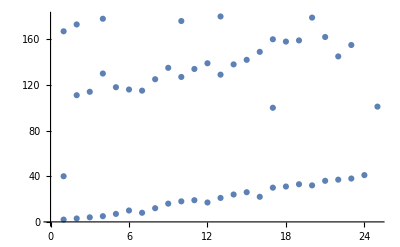

```mathematica
ListPlot[tax[[1,5]]]
```

```mathematica
RFassigns=outputgen2[[1]];
```

```mathematica
altinfo=Table[{i,RFassigns[[i,3,2]],Table[{RFassigns[[i,2,j]],fivetheaterdays[[RFassigns[[i,2,j]],5]],fivetheaterdays[[RFassigns[[i,2,j]],3]],fivetheaterdays[[RFassigns[[i,2,j]],4]]},{j,Length[RFassigns[[i,2]]]}]},{i,Length[RFassigns]}];
```

```mathematica
altanchinfo=Table[Select[altinfo,#[[2]]==i&],{i,i,23}];
```

```mathematica
lowaltindices=Table[DeleteCases[Table[If[Min[Table[altanchinfo[[i,j,3,k,2]],{k,Length[altanchinfo[[i,j,3]]]}]]≤18000.,altanchinfo[[i,j,1]],0],{j,Length[altanchinfo[[i]]]}],0],{i,23}];
highaltindices=Table[DeleteCases[Table[If[Min[Table[altanchinfo[[i,j,3,k,2]],{k,Length[altanchinfo[[i,j,3]]]}]]>18000.,altanchinfo[[i,j,1]],0],{j,Length[altanchinfo[[i]]]}],0],{i,23}];
```

```mathematica
altitudeindices=Table[{lowaltindices[[i]],highaltindices[[i]]},{i,23}];
```

```mathematica
eventsfromlowindices=Table[eventsfromindices[lowaltindices[[i,j]],fivetheaterdays,RFassigns],{i,23},{j,Length[lowaltindices[[i]]]}];
```

```mathematica
eventsfromhighindices=Table[eventsfromindices[highaltindices[[i,j]],fivetheaterdays,RFassigns],{i,23},{j,Length[highaltindices[[i]]]}];
```

```mathematica
highsets=Table[altchooser[eventsfromhighindices[[i]],altitudeindices[[i,2]],20,8],{i,23}];
hs=Table[DeleteCases[highsets[[i,j]],{}],{i,23},{j,2}];
```

```mathematica
lowsets=Table[altchooser[eventsfromlowindices[[i]],altitudeindices[[i,1]],20,7],{i,23}];
ls=Table[DeleteCases[lowsets[[i,j]],{}],{i,23},{j,2}];
```

```mathematica
tankeralts=Table[0,{i,Length[RFassigns]}];Do[tankeralts=sortiealtset[anchno,ls,hs,tankeralts],{anchno,23}]
```

```mathematica
sortiesmma=assembletheatersorties[RFassigns,fivetheaterdays,tankeralts];
```

numsorties = 180

```mathematica
altitudemissions=Table[sortiefuelburn[RFassigns,sortiesmma,i],{i,Length[RFassigns]}];
```

```mathematica
posspairelems=candidatetheatercombos[altitudemissions];
```

```mathematica
tscc=Sort[posspairelems,#2[[4]]>#1[[4]]&];
```

```mathematica
tries=DeleteCases[Flatten[Table[If[(diff=tscc[[j,3]]-tscc[[i,4]])>0&& diff<150, 
{Take[tscc[[i]],1],
Take[tscc[[j]],1]},0],{i,Length[tscc]-1},{j,i+1,Length[tscc]}],1],0];
```

```mathematica
visualprimitives[times_]:=Table[Line[{{times[[j,3]],10 times[[j,1]]},
{times[[j,4]],10 times[[j,1]]}}],{j,Length[times]}]
```

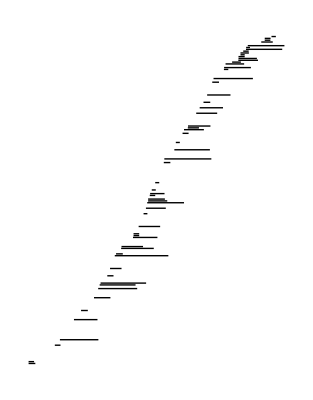

```mathematica
Graphics[visualprimitives[tscc]]
```

```mathematica
evals=Sort[DeleteCases[Table[horizontaltheatercomboevaluator[altitudemissions,RFassigns,tries[[i,1,1]],tries[[i,2,1]],startlatlongs,baselocs],{i,Length[tries]}],0],#2[[3]]>#1[[3]]&];
```

```mathematica
chosenpairs=pacman[evals]
```

length of list = 172

length of list = 166

length of list = 150

length of list = 139

length of list = 124

length of list = 110

length of list = 99

length of list = 91

length of list = 88

length of list = 86

length of list = 77

length of list = 65

length of list = 56

length of list = 50

length of list = 43

length of list = 35

length of list = 29

length of list = 18

length of list = 16

length of list = 12

length of list = 10

length of list = 6

length of list = 2

length of list = 0

{{65,111,21477.7,464,859},{61,93,21554.6,451,749},{155,168,21998.9,952,1285},{129,157,22805.2,797,1332},{122,131,22999.5,715,1134},{169,178,23531.9,1092,1396},{49,72,23744.9,372,676},{94,127,23774.4,583,981},{1,11,23799.8,-29,207},{37,64,24920.6,302,724},{86,130,27277.3,562,1048},{141,172,28292.5,903,1262},{83,118,28818.2,565,1086},{42,96,30776.4,330,785},{30,53,32510.8,232,563},{162,175,39822.4,1039,1500},{148,171,41980.1,944,1303},{165,179,46604.4,1013,1367},{44,100,46759.8,338,769},{138,167,52032.1,879,1319},{71,91,53192.1,537,803},{144,163,76579.4,931,1274},{166,177,90050.3,1066,1415},{170,180,107173.,1100,1400}}

```mathematica
chosenpairs=Sort[chosenpairs,#2[[4]]>#1[[4]]&]
```

{{1,11,23799.8,-29,207},{30,53,32510.8,232,563},{37,64,24920.6,302,724},{42,96,30776.4,330,785},{44,100,46759.8,338,769},{49,72,23744.9,372,676},{61,93,21554.6,451,749},{65,111,21477.7,464,859},{71,91,53192.1,537,803},{86,130,27277.3,562,1048},{83,118,28818.2,565,1086},{94,127,23774.4,583,981},{122,131,22999.5,715,1134},{129,157,22805.2,797,1332},{138,167,52032.1,879,1319},{141,172,28292.5,903,1262},{144,163,76579.4,931,1274},{148,171,41980.1,944,1303},{155,168,21998.9,952,1285},{165,179,46604.4,1013,1367},{162,175,39822.4,1039,1500},{166,177,90050.3,1066,1415},{169,178,23531.9,1092,1396},{170,180,107173.,1100,1400}}

```mathematica
combomissions=Table[combofuelburntheater[altitudemissions,RFassigns,chosenpairs[[i,1]],chosenpairs[[i,2]],startlatlongs,baselocs],{i,Length[chosenpairs]}];
```

```mathematica
comboevents=Sort[Table[{RFassigns[[chosenpairs[[i,1]],3,1]],RFassigns[[chosenpairs[[i,1]],3,2]],combomissions[[i,1,4]],combomissions[[i,-1,5]]},{i,Length[chosenpairs]}],#2[[3]]>#1[[3]]&]
```

{{4,23,-29,203},{5,12,232,556},{5,4,302,720},{2,16,330,760},{2,16,338,760},{2,2,372,657},{4,23,451,738},{2,7,464,836},{4,20,537,791},{3,18,562,1013},{3,8,565,1059},{3,18,583,950},{1,10,715,1091},{5,14,797,1300},{5,5,879,1303},{4,21,903,1251},{4,23,931,1262},{4,21,944,1275},{5,12,952,1281},{2,10,1013,1361},{5,1,1039,1472},{2,13,1066,1395},{2,2,1092,1377},{2,10,1100,1390}}

```mathematica
deletelist=Flatten[Table[{{chosenpairs[[i,1]]},{chosenpairs[[i,2]]}},{i,Length[chosenpairs]}],1]
```

{{1},{11},{30},{53},{37},{64},{42},{96},{44},{100},{49},{72},{61},{93},{65},{111},{71},{91},{86},{130},{83},{118},{94},{127},{122},{131},{129},{157},{138},{167},{141},{172},{144},{163},{148},{171},{155},{168},{165},{179},{162},{175},{166},{177},{169},{178},{170},{180}}

```mathematica
remaininglist=Delete[Table[i,{i,Length[altitudemissions]}],deletelist]
```

{2,3,4,5,6,7,8,9,10,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,31,32,33,34,35,36,38,39,40,41,43,45,46,47,48,50,51,52,54,55,56,57,58,59,60,62,63,66,67,68,69,70,73,74,75,76,77,78,79,80,81,82,84,85,87,88,89,90,92,95,97,98,99,101,102,103,104,105,106,107,108,109,110,112,113,114,115,116,117,119,120,121,123,124,125,126,128,132,133,134,135,136,137,139,140,142,143,145,146,147,149,150,151,152,153,154,156,158,159,160,161,164,173,174,176}

```mathematica
altitudemissionsminuscombos=Delete[altitudemissions,deletelist];
```

```mathematica
combomissions[[2]]
```

{{KGTF,,,232,278,0,0,0,200000.,185162,0,0,0,0,0,0},{,,ANCH12,288,315,25000,81600.,0,185162,96902,1925,4735,714.,1.,CAF,E8C},{0,ANCH12,ANCH13,315,334,0,0,0,96902,93518,3384,0,0,0,0,0},{,,ANCH13,447,500,25000,25500.,0,93518,43077.,17132,7809,99.,6.,CAF,F18},{,KGTF,,500,556,0,0,0,43077.,35520.,0,0,0,0,0,0}}

```mathematica
retainedmissions=Table[altitudemissions[[remaininglist[[i]]]],{i,Length[remaininglist]}];
```

```mathematica
allmissions=Join[retainedmissions,combomissions];
```

```mathematica
Length[allmissions]
```

156

```mathematica
allmissions[[137]]
```

{{KBIL,,,338,380,0,0,0,200000.,186008,0,0,0,0,0,0},{,,ANCH16,390,410,27000,17100.,0,186008,163223,1924,3761,82.,4.,CAF,F18},{,,ANCH16,439,459,27000,17100.,0,163223,137213,5362,3548,78.,4.,CAF,F18},{,,ANCH16,496,529,27000,17000.,0,137213,108367,6393,5453,84.,4.,CAF,F18},{,,ANCH16,557,577,27000,17100.,0,108367,83763,4440,3064,85.,4.,CAF,F18},{0,ANCH16,ANCH01,577,638,0,0,0,83763,75023,8740,0,0,0,0,0},{,,ANCH01,695,707,25000,8500.,0,75023,56434.,8352,1737,183.,2.,CAF,F16C},{,KBIL,,707,760,0,0,0,56434.,48878.,0,0,0,0,0,0}}

```mathematica
eventlist[singlemissions_,singlelist_,tankerRFs_]:=Join[Table[{i, tankerRFs[[singlelist[[i]],3,1]],tankerRFs[[singlelist[[i]],3,2]],singlemissions[[singlelist[[i]],1,4]],-1},{i,Length[singlelist]}],
Table[{i, tankerRFs[[singlelist[[i]],3,1]],tankerRFs[[singlelist[[i]],3,2]],singlemissions[[singlelist[[i]],-1,5]],1},{i,Length[singlelist]}],
Table[{i, tankerRFs[[singlelist[[i]],3,1]],tankerRFs[[singlelist[[i]],3,2]],singlemissions[[singlelist[[i]],-1,5]]+255,2},{i,Length[singlelist]}]]
```

```mathematica
eventlistcombo[comboevents_,singlelist_]:=
Join[Table[{i+Length[singlelist],comboevents[[i,1]],comboevents[[i,2]],comboevents[[i,3]],-1},{i,Length[comboevents]}],
Table[{i+Length[singlelist],comboevents[[i,1]],comboevents[[i,2]],comboevents[[i,4]],1},{i,Length[comboevents]}],
Table[{i+Length[singlelist],comboevents[[i,1]],comboevents[[i,2]],comboevents[[i,4]]+255,2},{i,Length[comboevents]}]]
```

```mathematica
singleevents[[2]]
```

Part::partd: Part specification singleevents⟦2⟧ is longer than depth of object.

singleevents⟦2⟧

```mathematica
comboevents[[2]]
```

{5,12,232,556}

```mathematica
singleevents=eventlist[altitudemissions,remaininglist,RFassigns];
```

```mathematica
doubleevents=eventlistcombo[comboevents,remaininglist];
```

```mathematica
allevents=Sort[Join[singleevents,doubleevents],#2[[4]]>#1[[4]]&];
```

```mathematica
ta2=tailassign[allevents,{40,40,40,40,40}];
```

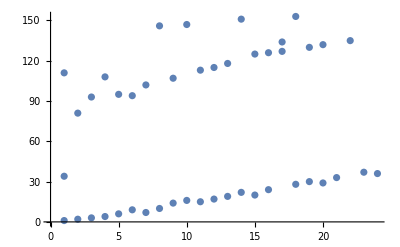

```mathematica
ListPlot[ta2[[1,5]]]
```

```mathematica
totaltails[ta2[[1]]]
```

111

```mathematica
mt2=missiontails[ta2[[1]]];
```

```mathematica
singlealtitudemissionCSV=formatnoncombines[retainedmissions,mt2];
```

```mathematica
sam=Dimensions[singlealtitudemissionCSV][[1]]
```

132

```mathematica
computesortiestats[allmissions,mt2,sam]
```

{SORTIE,20,132,917ARS,1,K135RT,KGTF,KGTF,JAN 23 20:00,JAN 24 00:40,200.,30.488,51.012,0.,10.488,04:40,JAN 24 04:55,SORTIE,Null,Null,Null,JAN 23 20:00,JAN 24 00:40,Null,Null,Null,Null,Null,-118.5,Null}

```mathematica
doublealtitudemissionCSV=formatcombines[allmissions,mt2,baselocs,anchorlist,sam];
```

```mathematica
Dimensions[doublealtitudemissionCSV]
```

{24,8}

```mathematica
allmissionsCSV=Join[singlealtitudemissionCSV,doublealtitudemissionCSV];
```

```mathematica
Do[allmissionsCSV[[i,1,1,2]]=mt2[[i,2]],{i,Length[allmissionsCSV]}];
```

```mathematica
missionoutCSV=Flatten[Table[Flatten[allmissionsCSV[[i]],1],{i,Length[allmissionsCSV]}],1];
```

```mathematica
Export["AltitudePlusHorizontalBasesImpinged.csv", missionoutCSV];
```

```mathematica
Dimensions[missionoutCSV]
```

{1395,30}